## Practise 9: group 2. Nerea Andia, Ander Cano, Mikel Lamela and Aitor Larrinoa.

## 9.1 Spectral Fourier Differentiation Matrices

### a) Write a program in Mathematica that computes the first and second derivatives, using commands ToeplitzMatrix in order to construct (9.2) and (9.3).

#### N = 20

```mathematica
(*  Set up grid and the differentiation matrix: *)
Clear["Global`*"]
NN=20; (* EVEN *)
h=2*Pi/NN;
x=Table[h*i,{i,1,NN}];
(*Now, we are going to calculate the Fourier differentiation matrix for first derivative*)
column1=Table[.5*(-1)^(i)*Cot[i*h/2],{i,1,NN-1}];
column1= Prepend[column1,0.];
column2=Table[.5*(-1)^(i)*Cot[i*h/2],{i,NN-1,1,-1}];
column2= Prepend[column2,0.];
DD1=ToeplitzMatrix[column1,column2]; (* Be careful, the two columns are needed  *)
MatrixForm[DD1];
```

```mathematica
(*Now, we are going to calculate the Fourier differentiation matrix for second order derivative*)
```

```mathematica
column3=Table[-(-1)^(i)/(2*(Sin[i*h/2]^2)),{i,1,NN-1}];
column3= Prepend[column3,-Pi^2/(3*h^2)-1/6];
column4=Table[-(-1)^(i)/(2*(Sin[i*h/2]^2)),{i,NN-1,1,-1}];
column4= Prepend[column4,-Pi^2/(3*h^2)-1/6];
DD2=ToeplitzMatrix[column3,column4]; (* Be careful, the two columns are needed  *)
MatrixForm[DD2];
```

```mathematica
(*  Differentiation of Exp(Sin(x)(Cos(x))^2): *)
v[y_]:= Exp[Sin[y] Cos[y]^2];
(*First derivative*)
derv1[y_]= D[v[y],y];
(*Second derivative*)
derv2[y_]=D[v[y],{y,2}]
(*Plot of the f function and its derivatives computed using the command D*)
Plot1=Plot[v[y],{y,0,2 Pi}, PlotStyle-> {Red,Dashed,Thick},PlotLabel->"Original function N = 20",PlotLegends->{"Exact Original function"}];
Plot2=Plot[{derv1[y]},{y,0,2 Pi}, PlotStyle->  {Blue,Dashed,Thick},PlotLabel->"First derivative N = 20",PlotLegends->{"Exact First derivative"}];
Plot3=Plot[{derv2[y]},{y,0,2 Pi}, PlotStyle->  {Green,Dashed,Thick},PlotLabel->"Second derivative N = 20",PlotLegends->{"Exact Second derivative"}];
```

ⅇ^(Cos[y]^2 Sin[y]) (Cos[y]^3-2 Cos[y] Sin[y]^2)^2+ⅇ^(Cos[y]^2 Sin[y]) (-7 Cos[y]^2 Sin[y]+2 Sin[y]^3)

```mathematica
numv = Table[v[h*i],{i,1,NN}];
derv1num = Table[derv1[h*i],{i,1,NN}];
derv2num = Table[derv2[h*i],{i,1,NN}];
MatrixForm[%];

numderv1 =Table[0,{i,1,NN}];
numderv1 = Dot[DD1,numv] //N;
numderv2 =Table[0,{i,1,NN}];
numderv2 = Dot[DD2,numv] //N;
MatrixForm[%];

numv=Prepend[numv,numv[[NN]]];
numderv11=Prepend[numderv1,numderv1[[NN]]];
MatrixForm[%];
numv2=Prepend[numv,numv[[NN]]];
numderv22=Prepend[numderv2,numderv2[[NN]]];
MatrixForm[%];
(*Now, we are going to plot the approximated derivatives using Fourier Differentiation Matrices*)
Plot4 = ListPlot[numv,PlotMarkers->{Automatic,Small},Joined->True,DataRange->{0,2 Pi},PlotLabel->"Original function N = 20",PlotLegends->{"Approx Original function"}];
Plot5 = ListPlot[numderv11,PlotMarkers->{Automatic,Small},Joined->True,DataRange->{0,2 Pi},PlotLabel->"First derivative N = 20",PlotLegends->{"Approx First derivative"}];
Plot6=ListPlot[numderv22,PlotMarkers->{Automatic,Small},Joined->True,DataRange->{0,2 Pi},PlotLabel->"Second derivative N = 20",PlotLegends->{"Approx Second derivative"}];
```

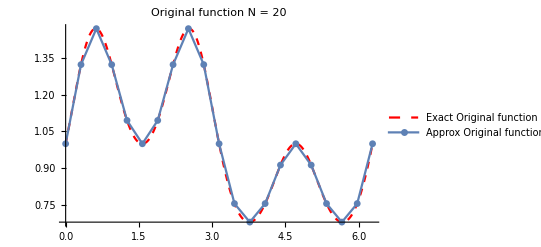

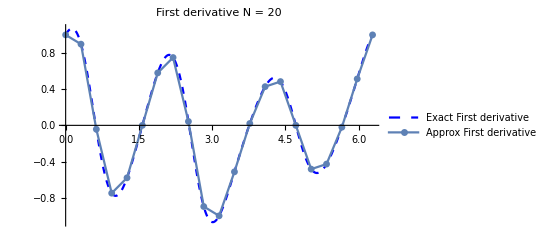

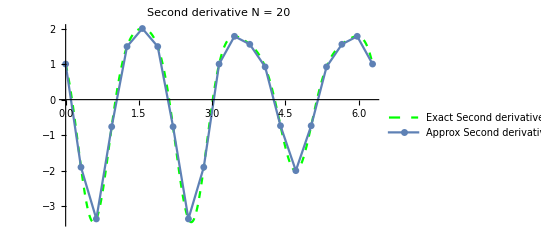

```mathematica
(*We show the plots in order to compare the results*)
Show[Plot1, Plot4]
Show[Plot2, Plot5]
Show[Plot3,Plot6]
```

```mathematica
(*Minimum and maximum values of the error of the first and second derivatives*)
Abs[numderv1-derv1num];
errormin11 = Min[Abs[numderv1-derv1num]]
errormax11 = Max[Abs[numderv1-derv1num]]
Abs[numderv2-derv2num];
errormin12 = Min[Abs[numderv1-derv1num]]
errormax12 = Max[Abs[numderv2-derv2num]]
```

0.

0.000410565

0.

0.00174695

#### N=60

```mathematica
(*  Set up grid and the differentiation matrix: *)
Clear["Global`*"]
NN=60; (* EVEN *)
h=2*Pi/NN;
x=Table[h*i,{i,1,NN}];
(*Now, we are going to calculate the Fourier differentiation matrix for first derivative*)
column1=Table[.5*(-1)^(i)*Cot[i*h/2],{i,1,NN-1}];
column1= Prepend[column1,0.];
column2=Table[.5*(-1)^(i)*Cot[i*h/2],{i,NN-1,1,-1}];
column2= Prepend[column2,0.];
DD1=ToeplitzMatrix[column1,column2]; (* Be careful, the two columns are needed  *)
MatrixForm[DD1];
```

```mathematica
(*Now, we are going to calculate the Fourier differentiation matrix for second order derivative*)
```

```mathematica
column3=Table[-(-1)^(i)/(2*(Sin[i*h/2]^2)),{i,1,NN-1}];
column3= Prepend[column3,-Pi^2/(3*h^2)-1/6];
column4=Table[-(-1)^(i)/(2*(Sin[i*h/2]^2)),{i,NN-1,1,-1}];
column4= Prepend[column4,-Pi^2/(3*h^2)-1/6];
DD2=ToeplitzMatrix[column3,column4]; (* Be careful, the two columns are needed  *)
MatrixForm[DD2];
```

```mathematica
(*  Differentiation of Exp(Sin(x)(Cos(x))^2): *)
v[y_]:= Exp[Sin[y] Cos[y]^2];
(*First derivative*)
derv1[y_]= D[v[y],y];
(*Second derivative*)
derv2[y_]=D[v[y],{y,2}]
(*Plot of the f function and its derivatives computed using the command D*)
Plot1=Plot[v[y],{y,0,2 Pi}, PlotStyle-> {Red,Dashed,Thick},PlotLabel->"Original function N = 60",PlotLegends->{"Exact Original function"}];
Plot2=Plot[{derv1[y]},{y,0,2 Pi}, PlotStyle->  {Blue,Dashed,Thick},PlotLabel->"First derivative N = 60",PlotLegends->{"Exact First derivative"}];
Plot3=Plot[{derv2[y]},{y,0,2 Pi}, PlotStyle->  {Green,Dashed,Thick},PlotLabel->"Second derivative N = 60",PlotLegends->{"Exact Second derivative"}];
```

ⅇ^(Cos[y]^2 Sin[y]) (Cos[y]^3-2 Cos[y] Sin[y]^2)^2+ⅇ^(Cos[y]^2 Sin[y]) (-7 Cos[y]^2 Sin[y]+2 Sin[y]^3)

```mathematica
numv = Table[v[h*i],{i,1,NN}];
derv1num = Table[derv1[h*i],{i,1,NN}];
derv2num = Table[derv2[h*i],{i,1,NN}];
MatrixForm[%];

numderv1 =Table[0,{i,1,NN}];
numderv1 = Dot[DD1,numv] //N;
numderv2 =Table[0,{i,1,NN}];
numderv2 = Dot[DD2,numv] //N;
MatrixForm[%];

numv=Prepend[numv,numv[[NN]]];
numderv11=Prepend[numderv1,numderv1[[NN]]];
MatrixForm[%];
numv2=Prepend[numv,numv[[NN]]];
numderv22=Prepend[numderv2,numderv2[[NN]]];
MatrixForm[%];
(*Now, we are going to plot the approximated derivatives using Fourier Differentiation Matrices*)
Plot4 = ListPlot[numv,PlotMarkers->{Automatic,Small},Joined->True,DataRange->{0,2 Pi},PlotLabel->"Original function N = 60",PlotLegends->{"Approx Original function"}];
Plot5 = ListPlot[numderv11,PlotMarkers->{Automatic,Small},Joined->True,DataRange->{0,2 Pi},PlotLabel->"First derivative N = 60",PlotLegends->{"Approx First derivative"}];
Plot6=ListPlot[numderv22,PlotMarkers->{Automatic,Small},Joined->True,DataRange->{0,2 Pi},PlotLabel->"Second derivative N = 60",PlotLegends->{"Approx Second derivative"}];
```

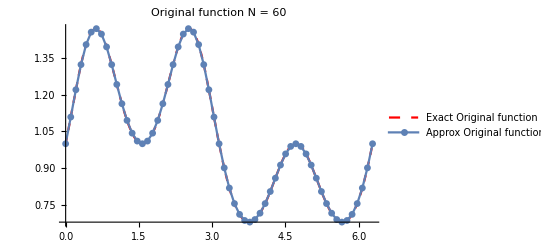

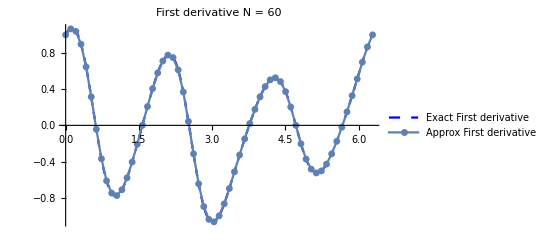

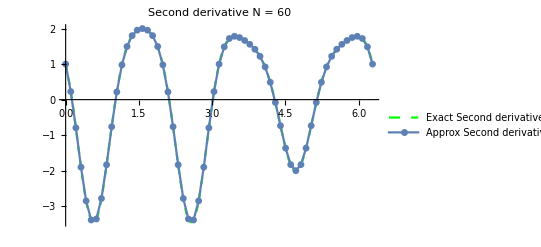

```mathematica
(*We show the plots in order to compare the results*)
Show[Plot1, Plot4]
Show[Plot2, Plot5]
Show[Plot3,Plot6]
```

```mathematica
(*Minimum and maximum values of the error of the first and second derivatives*)
Abs[numderv1-derv1num];
errormin11 = Min[Abs[numderv1-derv1num]]
errormax11 = Max[Abs[numderv1-derv1num]]
Abs[numderv2-derv2num];
errormin12 = Min[Abs[numderv1-derv1num]]
errormax12 = Max[Abs[numderv2-derv2num]]
```

0.

7.10543×10^-15

0.

1.64313×10^-13

## 9.2 Spectral Chebyshev Differentiation Matrices

### a) Write a program in Mathematica that computes the first and second derivatives, constructing the Chebyshev matrix using (9.5) and (9.6)

#### N = 20

```mathematica
(*  Set up grid and the differentiation matrix: *)
Clear["Global`*"]
NN=20;

h2 = Pi/NN;
x=Table[N[Cos[h2*i]],{i,0,NN}];
(*Chebyshev spectral diff matrix*)
MatCheb:=MatCheb=Table[0, {i,1,NN+1}, {j,1,NN+1}]
MatrixForm[MatCheb];
```

```mathematica
MatCheb[[1,1]]= N[(2NN^2 + 1)/6];
MatCheb[[NN+1,NN+1]]= -N[(2NN^2 + 1)/6];
MatCheb[[1,NN+1]]= 0.5 (-1)^NN;
MatCheb[[NN+1,1]]= -0.5 (-1)^NN;
For[i=2,i≤ NN,i++,
For[j=2,j≤ NN,j++,
If[i≠j,
MatCheb[[i,j]]=(-1)^(i-1+j-1) / (x[[i]]-x[[j]])]
]]
MatrixForm[MatCheb];
For[i=2,i≤ NN,i++,
MatCheb[[i,i]]=N[-x[[i]]/(2(1-x[[i]]^2))]
]
For[j=2,j≤ NN,j++,
MatCheb[[1,j]]=2 (-1)^(j-1) / (1-x[[j]])
]
For[i=2,i≤ NN,i++,
MatCheb[[i,1]]=-0.5 (-1)^(i-1) / (1-x[[i]])
]
For[j=2,j≤ NN,j++,
MatCheb[[NN+1,j]]=-2 (-1)^(NN+j-1) / (1+x[[j]])
]
For[i=2,i≤ NN,i++,
MatCheb[[i,NN+1]]=0.5 (-1)^(NN+i-1) / (1+x[[i]])
]

MatrixForm[MatCheb];
```

```mathematica
(*  Differentiation of v[y_]:= Exp[y] Sin[5y]  
v[y_]:= Exp[Sin[y]]; 
*)

v[y_]:=Exp [Sin[y](Cos[y])^2 ]
(*First derivative*)
derv1[y_]= D[v[y],y];
(*Second derivative*)
derv2[y_]= D[v[y],{y,2}];
(*Plots of the exact sol using command D*)
Plot1=Plot[v[y],{y,-1,1}, PlotStyle-> {Red,Dashed,Thick}, PlotRange-> All, PlotLabel-> "Original function N = 20",PlotLegends->{"Exact Original function"}];
Plot2=Plot[{derv1[y]},{y,-1,1}, PlotStyle->  {Blue,Dashed,Thick}, PlotRange-> All, PlotLabel-> "First derivative N = 20",PlotLegends->{"Exact First derivative"}];
Plot3=Plot[{derv2[y]},{y,-1,1}, PlotStyle->  {Purple,Dashed,Thick}, PlotRange-> All, PlotLabel-> "Second derivative N = 20",PlotLegends->{"Exact Second derivative"}];

numv = Table[N[v[x[[i]]]],{i,1,NN+1}];
MatrixForm[%];
derv1num = Table[N[derv1[x[[i]]]],{i,1,NN+1}];
MatrixForm[%];
derv2num = Table[N[derv2[x[[i]]]],{i,1,NN+1}];
MatrixForm[%];
(*Plot of the approximated sol*)
Plot4 = ListPlot[Table[{x[[i]],numv[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1}, PlotRange-> All,PlotStyle-> {Dotted, Green}, PlotLabel-> "Original function N = 20",PlotLegends->{"Approx Original function"}];
Plot5 = ListPlot[Table[{x[[i]],derv1num[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1}, PlotRange-> All,PlotStyle-> {Dotted, Green}, PlotLabel-> "First derivative N = 20",PlotLegends->{"Approx First derivative"}];
Plot6 = ListPlot[Table[{x[[i]],derv2num[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1}, PlotRange-> All,PlotStyle-> {Dotted, Green}, PlotLabel-> "Second derivative N = 20",PlotLegends->{"Approx Second derivative"}];
```

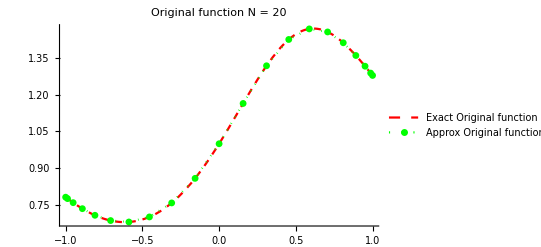

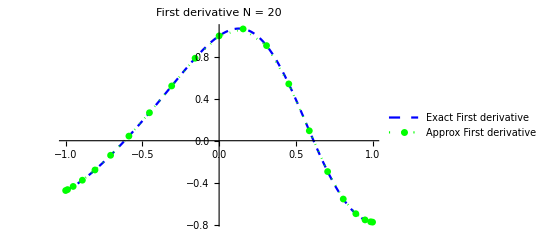

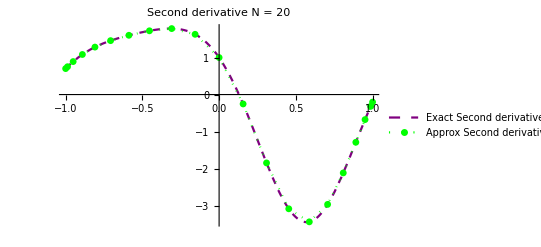

```mathematica
(*We compare the results obtained*)
Show[Plot1, Plot4]
Show[Plot2, Plot5]
Show[Plot3,Plot6]
```

```mathematica
numderv1 =Table[0,{i,1,NN+1}];

numderv1 = Dot[MatCheb,numv] //N;
MatrixForm[%];
numderv2 =Table[0,{i,1,NN+1}];

numderv2= Dot[MatCheb,numderv1] //N;
MatrixForm[%];

Plot7= ListPlot[Table[{x[[i]],numderv1[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle-> Orange];
Plot8= ListPlot[Table[{x[[i]],numderv2[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle-> Orange];
```

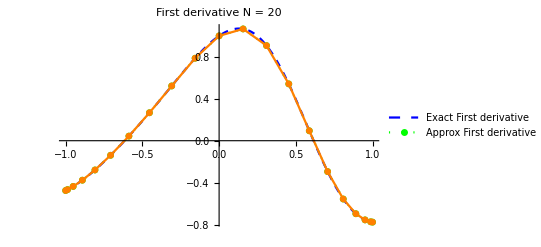

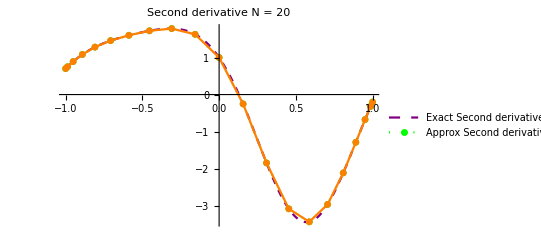

```mathematica
Show[Plot2, Plot5, Plot7]

Show[Plot3, Plot6, Plot8]
```

8.398×10^-8

2.57123×10^-7

3.28439×10^-9

0.0000684163

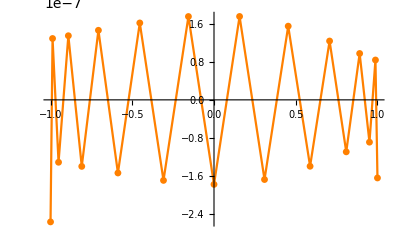

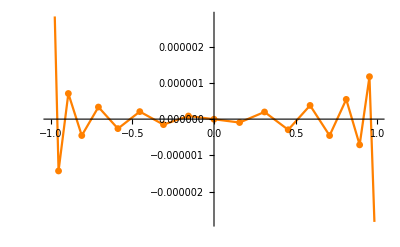

```mathematica
(*We calculate the maximum and minimum values of the error for the first and second derivatives*)
error21=numderv1-derv1num;
errormin21 = Min[Abs[error21]]
errormax21 = Max[Abs[error21]]

error22=numderv2-derv2num;
errormin22 = Min[Abs[error22]]
errormax22 = Max[Abs[error22]]

ListPlot[Table[{x[[i]],error21[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle-> Orange]
ListPlot[Table[{x[[i]],error22[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle-> Orange]
```

#### N = 60

```mathematica
(*  Set up grid and the differentiation matrix: *)
Clear["Global`*"]
NN=60;

h2 = Pi/NN;
x=Table[N[Cos[h2*i]],{i,0,NN}];
(*Chebyshev spectral diff matrix*)
MatCheb:=MatCheb=Table[0, {i,1,NN+1}, {j,1,NN+1}]
MatrixForm[MatCheb];
```

```mathematica
MatCheb[[1,1]]= N[(2NN^2 + 1)/6];
MatCheb[[NN+1,NN+1]]= -N[(2NN^2 + 1)/6];
MatCheb[[1,NN+1]]= 0.5 (-1)^NN;
MatCheb[[NN+1,1]]= -0.5 (-1)^NN;
For[i=2,i≤ NN,i++,
For[j=2,j≤ NN,j++,
If[i≠j,
MatCheb[[i,j]]=(-1)^(i-1+j-1) / (x[[i]]-x[[j]])]
]]
MatrixForm[MatCheb];
For[i=2,i≤ NN,i++,
MatCheb[[i,i]]=N[-x[[i]]/(2(1-x[[i]]^2))]
]
For[j=2,j≤ NN,j++,
MatCheb[[1,j]]=2 (-1)^(j-1) / (1-x[[j]])
]
For[i=2,i≤ NN,i++,
MatCheb[[i,1]]=-0.5 (-1)^(i-1) / (1-x[[i]])
]
For[j=2,j≤ NN,j++,
MatCheb[[NN+1,j]]=-2 (-1)^(NN+j-1) / (1+x[[j]])
]
For[i=2,i≤ NN,i++,
MatCheb[[i,NN+1]]=0.5 (-1)^(NN+i-1) / (1+x[[i]])
]

MatrixForm[MatCheb];
```

```mathematica
(*  Differentiation of v[y_]:= Exp[y] Sin[5y]  
v[y_]:= Exp[Sin[y]]; 
*)

v[y_]:=Exp [Sin[y](Cos[y])^2 ]
(*First derivative*)
derv1[y_]= D[v[y],y];
(*Second derivative*)
derv2[y_]= D[v[y],{y,2}];
(*Plots of the exact sol using command D*)
Plot1=Plot[v[y],{y,-1,1}, PlotStyle-> {Red,Dashed,Thick}, PlotRange-> All, PlotLabel-> "Original function N = 60",PlotLegends->{"Exact Original function"}];
Plot2=Plot[{derv1[y]},{y,-1,1}, PlotStyle->  {Blue,Dashed,Thick}, PlotRange-> All, PlotLabel-> "First derivative N = 60",PlotLegends->{"Exact First derivative"}];
Plot3=Plot[{derv2[y]},{y,-1,1}, PlotStyle->  {Purple,Dashed,Thick}, PlotRange-> All, PlotLabel-> "Second derivative N = 60",PlotLegends->{"Exact Second derivative"}];

numv = Table[N[v[x[[i]]]],{i,1,NN+1}];
MatrixForm[%];
derv1num = Table[N[derv1[x[[i]]]],{i,1,NN+1}];
MatrixForm[%];
derv2num = Table[N[derv2[x[[i]]]],{i,1,NN+1}];
MatrixForm[%];
(*Plot of the approximated sol*)
Plot4 = ListPlot[Table[{x[[i]],numv[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1}, PlotRange-> All,PlotStyle-> {Dotted, Green}, PlotLabel-> "Original function N = 60",PlotLegends->{"Approx Original function"}];
Plot5 = ListPlot[Table[{x[[i]],derv1num[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1}, PlotRange-> All,PlotStyle-> {Dotted, Green}, PlotLabel-> "First derivative N = 60",PlotLegends->{"Approx First derivative"}];
Plot6 = ListPlot[Table[{x[[i]],derv2num[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1}, PlotRange-> All,PlotStyle-> {Dotted, Green}, PlotLabel-> "Second derivative N = 60",PlotLegends->{"Approx Second derivative"}];
```

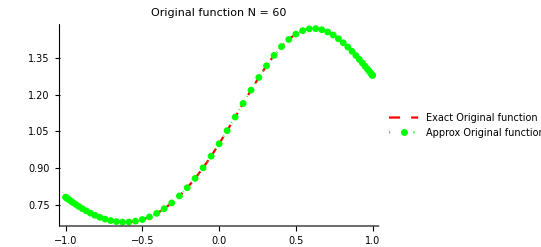

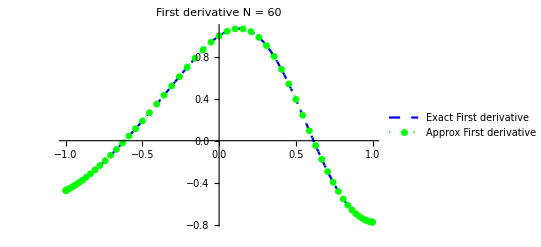

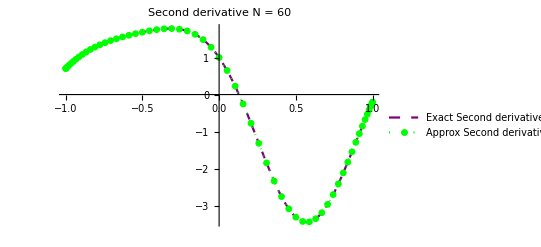

```mathematica
(*We compare the results obtained*)
Show[Plot1, Plot4]
Show[Plot2, Plot5]
Show[Plot3,Plot6]
```

```mathematica
numderv1 =Table[0,{i,1,NN+1}];

numderv1 = Dot[MatCheb,numv] //N;
MatrixForm[%];
numderv2 =Table[0,{i,1,NN+1}];

numderv2= Dot[MatCheb,numderv1] //N;
MatrixForm[%];

Plot7= ListPlot[Table[{x[[i]],numderv1[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle-> Orange];
Plot8= ListPlot[Table[{x[[i]],numderv2[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle->Orange];
```

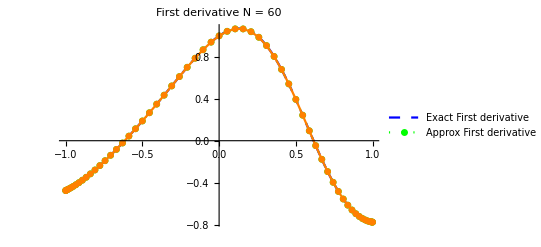

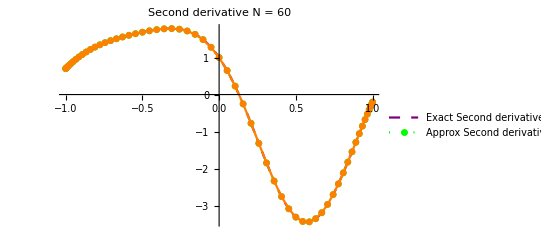

```mathematica
Show[Plot2, Plot5, Plot7]

Show[Plot3, Plot6, Plot8]
```

3.747×10^-16

5.11092×10^-11

4.41625×10^-11

6.2709×10^-8

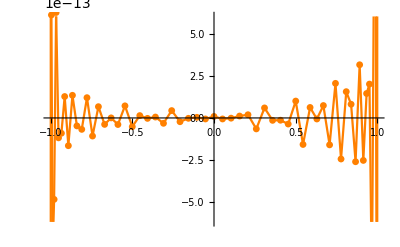

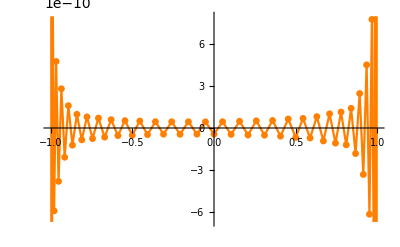

```mathematica
(*We calculate the maximum and minimum values of the error for the first and second derivatives*)
error21=numderv1-derv1num;
errormin21 = Min[Abs[error21]]
errormax21 = Max[Abs[error21]]

error22=numderv2-derv2num;
errormin22 = Min[Abs[error22]]
errormax22 = Max[Abs[error22]]

ListPlot[Table[{x[[i]],error21[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle-> Orange]
ListPlot[Table[{x[[i]],error22[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle-> Orange]
```

## 9.3 Chebyshev Series and FFT

### a) Modify the program (Spectral-example-trefethen-pag81-p18.nb), written in Mathematica, that computes the first derivative, using the algorithm for spectral Chebyshev differentiation defined as a Module

#### N = 60

```mathematica
Clear["Global`*"]
NN=60;h=Pi/NN;
x=Table[Cos[h*i],{i,0,NN}];
u0[y_]:=Exp [Sin[y](Cos[y])^2 ];
v = u0[x]; (* Generate a table with the NN values *)

derv1[y_]= D[u0[y],y];
derv2[y_]= D[u0[y],{y,2}];
d1v = derv1[x];  (* Generate a table with the NN values *)
d2v = derv2[x];

(*Plot of the original function and the first and second derivatives*)

Plot1=Plot[v[y],{y,-1,1}, PlotStyle-> {Red,Dashed,Thick}, PlotRange-> All, PlotLabel-> "Original function N = 60",PlotLegends->{"Exact Original function"}];
Plot2=Plot[{derv1[y]},{y,-1,1}, PlotStyle->  {Blue,Dashed,Thick}, PlotRange-> All, PlotLabel-> "First derivative N = 60",PlotLegends->{"Exact First derivative"}];
Plot3=Plot[{derv2[y]},{y,-1,1}, PlotStyle->  {Green,Dashed,Thick}, PlotRange-> All, PlotLabel-> "Second derivative N = 60",PlotLegends->{"Exact Second derivative"}];
```

```mathematica
ChebyshevDer[v_,x_,NN_]:=Module[{u,w,datav,datavhat,dataw,vect,vect1,vect2,what,suma0,suma1},
u= ConstantArray[0,2 NN];
For[j=1,j<=NN-1,j++,u[[2NN -j+1]]= v[[j+1]]];
w = Drop[u,NN+1];
datav=Join[v,w];
datavhat=Re[Fourier[datav,FourierParameters->{1,-1}]];
vect1=Table[j,{j,0, NN-1}];
vect2=Table[j,{j,-NN+1, -1}];
vect=Append[vect1,0.0];
vect=Flatten[Append[vect,vect2]];
what=I*vect*datavhat;
dataw=Re[InverseFourier[what,FourierParameters->{1,-1}]];
w= ConstantArray[0,NN+1];
For[j=2,j<=NN,j++,w[[j]]= -dataw[[j]]/Sqrt[1-x[[j]]^2]];
suma0=0.;
For[j=1,j<=NN-1,j++,suma0= suma0+j^2 datavhat[[j+1]]];
suma0 = suma0 + 0.5 NN^2 datavhat[[NN+1]];
w[[1]]=suma0/NN;
suma1=0;
For[j=1,j<=NN-1,j++,suma1= suma1+(-1)^(j+1) j^2 datavhat[[j+1]]];
suma1 = suma1 +0.5(-1)^(NN+1) NN^2 datavhat[[NN+1]];
w[[NN+1]]= suma1/NN;
w
]
```

```mathematica
Du=ChebyshevDer[v,x,NN];
DerivDu=ChebyshevDer[Du,x,NN];

(*Plot of the approximated solution of the original function and the first and second derivatives*)
Plot4=ListPlot[Table[{x[[j]], v[[j]]},{j,1,NN+1}],PlotMarkers->{Automatic,Small}, Joined-> True, PlotRange-> All,PlotStyle-> Purple, PlotLabel-> "Original function N = 60",PlotLegends->{"Approx Original function"}];
Plot5=ListPlot[Table[{x[[j]], d1v[[j]]},{j,1,NN+1}],PlotMarkers->{Automatic,Small}, Joined-> True, PlotRange-> All,PlotStyle-> Red, PlotLabel-> "First derivative N = 60",PlotLegends->{"Approx First derivative "}];
Plot6=ListPlot[Table[{x[[j]], d2v[[j]]},{j,1,NN+1}],PlotMarkers->{Automatic,Small}, Joined-> True, PlotRange-> All,PlotStyle-> Red, PlotLabel-> "Second derivative N = 60",PlotLegends->{"Approx Second derivative"}];
Plot7=ListPlot[Table[{x[[j]],Du[[j]]},{j,1,NN+1}],PlotMarkers->{Automatic,Small}, Joined-> True, PlotRange-> All,PlotStyle-> {Purple,Dashed}];
Plot8=ListPlot[Table[{x[[j]],DerivDu[[j]]},{j,1,NN+1}],PlotMarkers->{Automatic,Small}, Joined-> True, PlotRange-> All,PlotStyle-> {Purple,Dashed}];
```

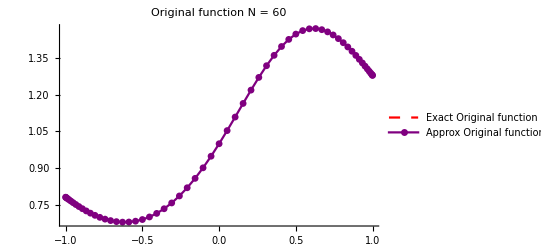

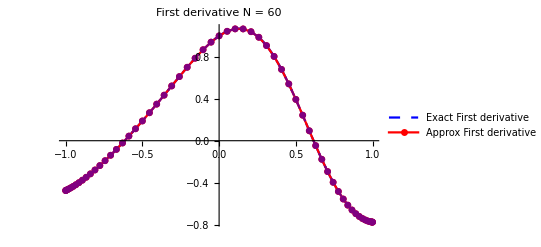

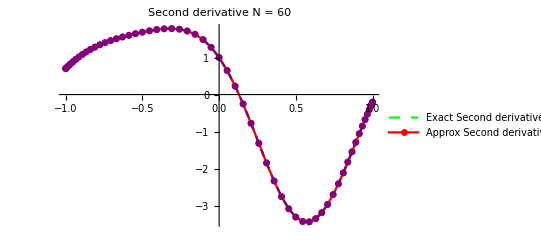

```mathematica
(*We compare now the exact solution and the approximated one*)

Show[Plot1,Plot4]
Show[Plot2,Plot5,Plot7]
Show[Plot3,Plot6, Plot8]
```

1.11022×10^-16

4.17222×10^-13

4.10783×10^-15

2.96436×10^-10

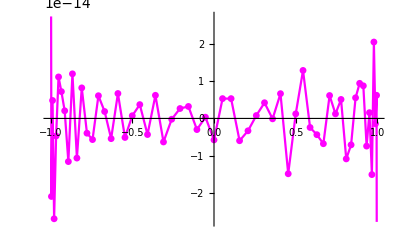

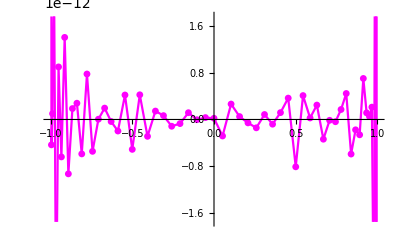

```mathematica
(*We calculate the maximum and minimum value of the error*)
error31=d1v-Du;
errormin31 = Min[Abs[error31]]
errormax31 = Max[Abs[error31]]
error32=DerivDu-d2v;
errormin32 = Min[Abs[error32]]
errormax32 = Max[Abs[error32]]

(*We plot the error*)
ListPlot[Table[{x[[i]],error31[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle->Magenta]
ListPlot[Table[{x[[i]],error32[[i]]},{i,1,NN+1}],PlotMarkers->{Automatic,Small},Joined->True,DataRange->{-1,1},PlotStyle-> Magenta]
```